```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* Definition of R in terms of N=Log[a] *)
Ra[Nn_]:=6(2 H[Nn]^2+H[Nn] H'[Nn])
(* Definition of the f(R) Lagrangian  *)
f[R_]:=R-2Λ (1-1/(1+(R /(b Λ))^n))/.Λ->3(1-om-or)H0^2
n=1;
```

```mathematica
(* Definition of the ODE in terms of N=Log[a]=-Log[1+z] *)
ODE=-f'[R]H[Nn]^2+HL[Nn]^2-H0^2(1-om-or)+0(om Exp[-3 Nn]+or Exp[-4 Nn])+1/6(f'[R]R-f[R])-f''[R]H[Nn]^2 Ra'[Nn]/.R->Ra[Nn]//Simplify;
```

```mathematica
HL[Nn_]:=H0 Sqrt[om Exp[-3 Nn]+or Exp[-4 Nn]+(1-om-or)]
```

```mathematica
(* Solve the ODE *)
h=0.704;
or0=0;
om0=.24;
H0=1;
modfried[om1_?NumberQ,b1_?NumberQ,Ns_?NumberQ]:=(modfried[om1,b1,Ns]=NDSolve[{(ODE/.om->om1/.b->b1/.or->or0//Evaluate)==0,H[Ns]==√(om0 Exp[-3 Ns]+or0 Exp[-4 Ns]+1-om0-or0),H'[Ns]==-(ⅇ^(-4 Ns) (3 ⅇ^Ns om0+4 or0))/(2 √(1+(-1+ⅇ^(-3 Ns)) om0+(-1+ⅇ^(-4 Ns)) or0))},H,{Nn,Ns,0},MaxSteps->2000000])
Hsol[Nn_?NumberQ,om1_?NumberQ,b1_?NumberQ,Ns_?NumberQ]:=(H[Nn]/.modfried[om1,b1,Ns][[1]])
Hsolp[Nn_?NumberQ,om1_?NumberQ,b1_?NumberQ,Ns_?NumberQ]:=(H'[Nn]/.modfried[om1,b1,Ns][[1]])
yH[Nn_?NumberQ,om1_?NumberQ,b1_?NumberQ,Ns_?NumberQ]:=((H[Nn]^2/om0-Exp[-3Nn]-or0/om0 Exp[-4Nn])/.modfried[om1,b1,Ns][[1]])
yHp[Nn_?NumberQ,om1_?NumberQ,b1_?NumberQ,Ns_?NumberQ]:=((3 ⅇ^(-3 Nn)+(4 ⅇ^(-4 Nn) or0)/om0+(2 H[Nn] H'[Nn])/om0)/.modfried[om1,b1,Ns][[1]])
```

```mathematica
Ns=Log[1/(1+30.)];
```

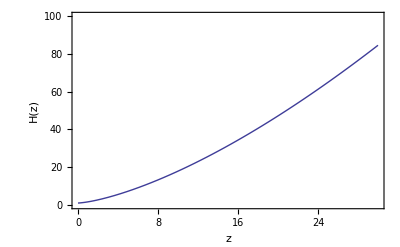

```mathematica
Plot[Hsol[Log[1/(1+z)],om0,.01,Ns],{z,0.,30.},PlotRange->{0,100},Frame->True,FrameLabel->{"z","H(z)"}]
```